### Fixed trails, changes made in code-03

Why isn’t trails showing up?

```mathematica
GraphicsGrid[CellularAutomatonCompositePlot[#,{"Static"->50,{"Trails",10,.9}->40,{"3D",6}->30},1]&/@{"Beehive","Block","Loaf"},Dividers->{False,All},FrameStyle->Opacity[.3]]
```

-Graphics-

### Exploring things to show in “What’s been made in game of life?”

#### zoom in on one pattern that shows different creations

For instance the gosper glider gun has gliders, spaceship and still lifes. Here is the traditional visualization

```mathematica
AnimationVideo[ArrayPlot[CellularAutomaton["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0}, {{{i}}, {-8, 20}, {-15, 45}}], Mesh->True,MeshStyle->Opacity[.1]], {i, 1, 100, 1}]
```

```mathematica
CellularAutomatonPlot3D["GameOfLife", {$LifeData["Gosper glider gun"]["MatrixData"], 0}, 50]
```

-Graphics3D-

```mathematica
ListAnimate[CellularAutomatonHistory["GameOfLife",$LifeData["Gosper glider gun"]["MatrixData"],60,Mesh->True,MeshStyle->Opacity[.1], ViewPoint->{2, -2, -1.5}, Boxed->False]]
```

```mathematica
CellularAutomatonInteractive3DPlot["GameOfLife",$LifeData["Gosper glider gun"]["MatrixData"],60,Mesh->True,MeshStyle->Opacity[.1], ViewPoint->{2, -2, -1.5}, Boxed->False]
```

```mathematica
"/Users/erichegonzales/Documents/Wolfram/Video/AnimationVideo-2025-02-18T20-01-01.mp4"
```

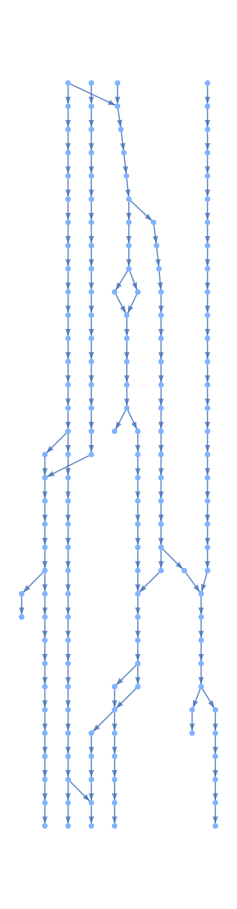

```mathematica
PatternsLayeredGraph[$LifeData["Gosper glider gun"]]
```

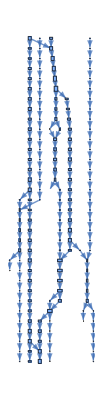

```mathematica
BoundingBoxLayeredGraph[$LifeData["Gosper glider gun"]]
```

#### May want to do period 15 gun instead

```mathematica
(CellularAutomatonPlot3D[
  "GameOfLife",{#,0},120,
  ColorFunction->(If[#==1,SetAlphaChannel[ RGBColor[1., 0.6436, 0.03622, 1.],1],Transparent] &),
  ColorFunctionScaling->False,ImageSize->1000,Mesh->True,MeshStyle->Opacity[.3]
])&/@(#MatrixData&/@Select[$LifeData,#Class==="Gun"&&#Period==15&]//Quiet)
```

<|Period-15 glider gun→-Graphics3D-|>

#### See “GameOfLife-02” for more glider examples

### Trying to understand dependency graph

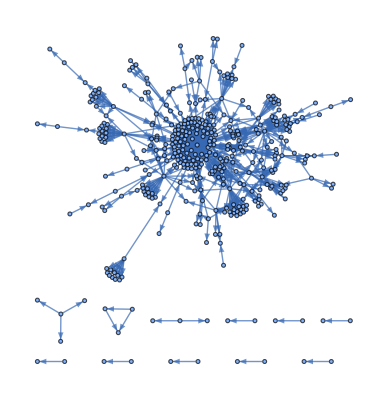

```mathematica
g2osc=InclusionsGraph["Oscillator","Oscillator"]
```

```mathematica
Keys[$LifeParts]
```

{Oscillator,Spaceship,Strict still life,Gun,Puffer,Induction coil,Reflector}

```mathematica
KeyValueMap[Labeled[ArrayPlot3D[Rest[#2]], #1]&, $LifeParts["Oscillator"][[;;10]]]
```

{-Graphics3D-101,-Graphics3D-104P9,-Graphics3D-106P135,-Graphics3D-110P62,-Graphics3D-112P15,-Graphics3D-112P23,-Graphics3D-112P57,-Graphics3D-116P101,-Graphics3D-120P34,-Graphics3D-1-2-3}

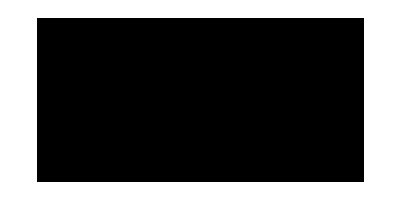
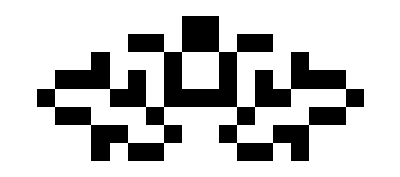

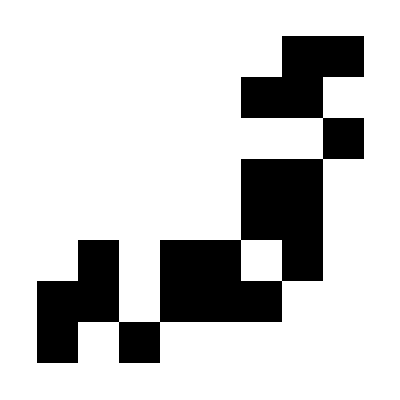
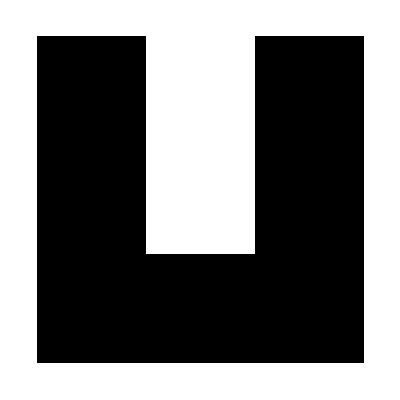
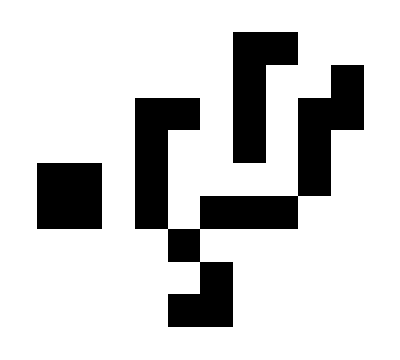
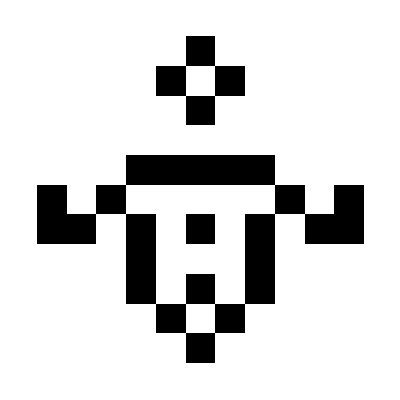
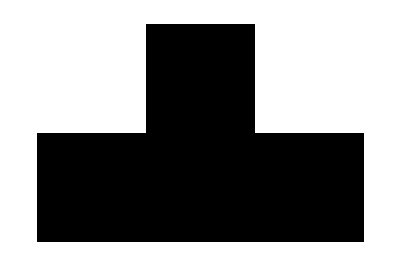
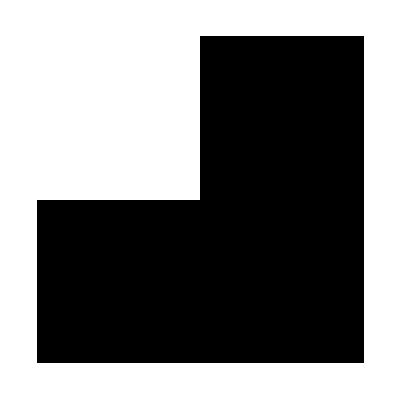
<|101→-Graphics-,104P9→-Graphics-,106P135→-Graphics-,110P62→-Graphics-,112P15→-Graphics-,112P23→-Graphics-,112P57→-Graphics-,116P101→-Graphics-,120P34→-Graphics-,1-2-3→-Graphics-,1-2-3-4→-Graphics-,123P27.1→-Graphics-,124P21→-Graphics-,128P10.2→-Graphics-,132P7→-Graphics-,134P25→-Graphics-,134P39.1→-Graphics-,145P20→-Graphics-,168P22.1→-Graphics-,180P8→-Graphics-,186P24→-Graphics-,204P41→-Graphics-,209P8→-Graphics-,20P4→-Graphics-,22P36→-Graphics-,22P4.3→-Graphics-,2.3.3→-Graphics-,246P41→-Graphics-,24P10→-Graphics-,255P132→-Graphics-|>

```mathematica
ArrayPlot/@$LifeParts["Oscillator"][[;;30, 1]]
```

```mathematica
KeyValueMap[Labeled[ArrayPlot3D[Rest[#2]], #1]&, $LifeParts["Oscillator"][[;;3]]]
```

```mathematica
mat=Boole[Outer[SubsetQ[#2,#1]&,
Values[$LifeParts["Oscillator"]],
Values[$LifeParts["Oscillator"]],
1]];
```

```mathematica
Outer[f, {1, 2, 3}, {4, 5, 6}]
```

{{f[1,4],f[1,5],f[1,6]},{f[2,4],f[2,5],f[2,6]},{f[3,4],f[3,5],f[3,6]}}

```mathematica
ArrayPlot[mat[[;;100]]]
```

-Graphics-

```mathematica
Select[Position[mat, 1], #[[1]] != #[[2]]&]
```

{{2,397},{2,623},{20,259},{25,434},{31,32},{42,197},{42,579},{44,341},{44,364},{44,400},{44,426},{44,428},{44,497},{44,498},{44,581},{44,583},{44,604},{44,645},{51,373},{51,427},{53,145},{53,580},{57,347},{60,13},{74,277},{74,452},{78,582},{79,145},{79,330},{79,375},{79,458},{81,310},{81,316},{81,359},{81,519},{81,588},{81,589},{86,411},{86,553},{90,3},{113,32},{124,384},{124,393},{126,595},{134,4},{134,8},{134,15},{134,25},{134,32},{134,54},{134,59},{134,64},{134,67},{134,68},{134,78},{134,83},{134,84},{134,93},{134,95},{134,99},{134,101},{134,107},{134,110},{134,113},{134,114},{134,145},{134,147},{134,153},{134,166},{134,202},{134,217},{134,221},{134,247},{134,254},{134,255},{134,256},{134,258},{134,260},{134,264},{134,266},{134,267},{134,268},{134,270},{134,277},{134,279},{134,283},{134,285},{134,286},{134,292},{134,293},{134,296},{134,297},{134,299},{134,300},{134,303},{134,304},{134,305},{134,307},{134,318},{134,319},{134,320},{134,326},{134,327},{134,331},{134,332},{134,338},{134,340},{134,343},{134,344},{134,345},{134,348},{134,349},{134,354},{134,355},{134,359},{134,360},{134,366},{134,385},{134,387},{134,392},{134,393},{134,401},{134,409},{134,415},{134,417},{134,419},{134,421},{134,431},{134,434},{134,441},{134,442},{134,460},{134,462},{134,464},{134,468},{134,475},{134,478},{134,483},{134,484},{134,486},{134,488},{134,490},{134,508},{134,512},{134,525},{134,526},{134,540},{134,541},{134,545},{134,547},{134,548},{134,550},{134,552},{134,555},{134,556},{134,557},{134,560},{134,562},{134,563},{134,565},{134,567},{134,569},{134,571},{134,572},{134,581},{134,582},{134,584},{134,589},{134,594},{134,597},{134,599},{134,600},{134,605},{134,608},{134,609},{134,611},{134,615},{134,616},{134,621},{134,623},{134,624},{134,626},{134,627},{134,629},{134,634},{134,636},{134,640},{134,641},{134,642},{134,643},{134,644},{134,646},{134,650},{134,651},{134,653},{134,657},{134,658},{134,668},{134,698},{134,699},{134,724},{134,756},{134,766},{137,383},{148,21},{149,13},{149,123},{149,165},{149,269},{149,293},{149,345},{149,543},{149,671},{149,680},{149,684},{152,335},{156,146},{156,257},{156,280},{156,334},{156,418},{156,420},{156,459},{156,472},{156,508},{156,534},{156,540},{156,579},{156,615},{156,632},{159,61},{159,83},{159,254},{159,261},{159,268},{159,278},{159,298},{159,301},{159,302},{159,319},{159,391},{159,451},{159,457},{159,476},{159,487},{159,512},{159,518},{159,601},{159,625},{159,632},{159,635},{160,82},{179,650},{182,402},{182,533},{184,152},{184,260},{184,262},{184,295},{184,335},{184,356},{184,377},{184,398},{184,410},{184,412},{184,449},{184,489},{184,491},{184,524},{184,525},{184,553},{184,554},{184,555},{184,556},{184,587},{184,589},{184,590},{184,592},{184,620},{184,633},{184,634},{184,637},{184,651},{184,652},{184,653},{184,678},{187,433},{187,599},{187,647},{187,654},{195,85},{195,111},{195,253},{195,263},{195,272},{195,281},{195,299},{195,331},{195,371},{195,422},{195,503},{195,546},{195,617},{195,629},{195,684},{195,744},{205,165},{205,311},{205,345},{205,355},{205,465},{205,511},{205,545},{205,587},{205,600},{205,671},{212,221},{212,255},{212,344},{212,385},{212,478},{212,512},{212,569},{212,600},{212,641},{212,746},{214,165},{214,218},{214,431},{214,527},{216,275},{216,635},{218,431},{220,545},{220,641},{223,260},{223,449},{223,450},{223,524},{223,525},{223,620},{223,633},{223,636},{223,652},{223,653},{223,655},{230,319},{230,567},{234,4},{234,85},{234,408},{234,550},{234,648},{234,698},{235,681},{238,16},{238,18},{238,263},{238,276},{238,299},{238,317},{238,372},{238,386},{238,425},{238,584},{238,597},{238,650},{239,191},{239,259},{239,371},{239,401},{239,412},{239,435},{239,450},{239,467},{239,507},{239,555},{239,744},{241,21},{241,148},{249,281},{249,503},{252,443},{252,521},{252,612},{271,331},{271,448},{324,446},{402,533},{459,632},{503,281},{507,259},{510,512},{532,523},{536,557},{538,3},{538,90},{574,258},{574,314},{574,519},{574,560},{574,607},{574,628},{576,359},{578,248},{578,316},{578,484},{665,3},{665,90},{665,93},{665,166},{665,228},{665,265},{665,294},{665,295},{665,344},{665,353},{665,406},{665,468},{665,469},{665,470},{665,533},{665,538},{665,539},{665,542},{665,543},{665,544},{665,546},{665,597},{665,598},{665,640},{665,641},{665,642},{665,643},{695,166},{695,208},{695,236},{695,292},{695,724},{701,283},{701,304},{701,306},{701,356},{701,413},{701,414},{701,526},{701,552},{701,617},{701,618},{701,621},{718,437},{723,486},{733,322},{733,646},{736,108},{737,311},{737,410},{737,513},{737,676},{741,637},{742,55},{742,69},{742,112},{742,255},{742,300},{742,343},{742,357},{742,437},{742,491},{742,509},{742,510},{742,512},{742,530},{742,533},{742,624},{742,654},{742,668},{744,371},{745,166},{745,202},{745,281},{745,344},{745,345},{745,371},{745,466},{745,467},{745,503},{745,526},{745,616},{745,617},{745,744},{746,255},{746,344},{746,385},{746,478},{746,512},{746,569},{746,600},{752,580},{754,471},{754,477},{754,646},{754,755},{754,756},{758,335},{762,70},{762,269},{762,293},{762,294},{762,302},{762,312},{762,319},{762,366},{762,367},{762,382},{762,430},{762,455},{762,456},{762,458},{762,537},{762,540},{762,541},{762,560},{762,573},{762,590},{762,607},{762,640},{762,697}}

```mathematica
Select[Position[mat, 1], #[[1]] != #[[2]]&]
```

{{2,397},{2,623},{20,259},{25,434},{31,32},{42,197},{42,579},{44,341},{44,364},{44,400},{44,426},{44,428},{44,497},{44,498},{44,581},{44,583},{44,604},{44,645},{51,373},{51,427},{53,145},{53,580},{57,347},{60,13},{74,277},{74,452},{78,582},{79,145},{79,330},{79,375},{79,458},{81,310},{81,316},{81,359},{81,519},{81,588},{81,589},{86,411},{86,553},{90,3},{113,32},{124,384},{124,393},{126,595},{134,4},{134,8},{134,15},{134,25},{134,32},{134,54},{134,59},{134,64},{134,67},{134,68},{134,78},{134,83},{134,84},{134,93},{134,95},{134,99},{134,101},{134,107},{134,110},{134,113},{134,114},{134,145},{134,147},{134,153},{134,166},{134,202},{134,217},{134,221},{134,247},{134,254},{134,255},{134,256},{134,258},{134,260},{134,264},{134,266},{134,267},{134,268},{134,270},{134,277},{134,279},{134,283},{134,285},{134,286},{134,292},{134,293},{134,296},{134,297},{134,299},{134,300},{134,303},{134,304},{134,305},{134,307},{134,318},{134,319},{134,320},{134,326},{134,327},{134,331},{134,332},{134,338},{134,340},{134,343},{134,344},{134,345},{134,348},{134,349},{134,354},{134,355},{134,359},{134,360},{134,366},{134,385},{134,387},{134,392},{134,393},{134,401},{134,409},{134,415},{134,417},{134,419},{134,421},{134,431},{134,434},{134,441},{134,442},{134,460},{134,462},{134,464},{134,468},{134,475},{134,478},{134,483},{134,484},{134,486},{134,488},{134,490},{134,508},{134,512},{134,525},{134,526},{134,540},{134,541},{134,545},{134,547},{134,548},{134,550},{134,552},{134,555},{134,556},{134,557},{134,560},{134,562},{134,563},{134,565},{134,567},{134,569},{134,571},{134,572},{134,581},{134,582},{134,584},{134,589},{134,594},{134,597},{134,599},{134,600},{134,605},{134,608},{134,609},{134,611},{134,615},{134,616},{134,621},{134,623},{134,624},{134,626},{134,627},{134,629},{134,634},{134,636},{134,640},{134,641},{134,642},{134,643},{134,644},{134,646},{134,650},{134,651},{134,653},{134,657},{134,658},{134,668},{134,698},{134,699},{134,724},{134,756},{134,766},{137,383},{148,21},{149,13},{149,123},{149,165},{149,269},{149,293},{149,345},{149,543},{149,671},{149,680},{149,684},{152,335},{156,146},{156,257},{156,280},{156,334},{156,418},{156,420},{156,459},{156,472},{156,508},{156,534},{156,540},{156,579},{156,615},{156,632},{159,61},{159,83},{159,254},{159,261},{159,268},{159,278},{159,298},{159,301},{159,302},{159,319},{159,391},{159,451},{159,457},{159,476},{159,487},{159,512},{159,518},{159,601},{159,625},{159,632},{159,635},{160,82},{179,650},{182,402},{182,533},{184,152},{184,260},{184,262},{184,295},{184,335},{184,356},{184,377},{184,398},{184,410},{184,412},{184,449},{184,489},{184,491},{184,524},{184,525},{184,553},{184,554},{184,555},{184,556},{184,587},{184,589},{184,590},{184,592},{184,620},{184,633},{184,634},{184,637},{184,651},{184,652},{184,653},{184,678},{187,433},{187,599},{187,647},{187,654},{195,85},{195,111},{195,253},{195,263},{195,272},{195,281},{195,299},{195,331},{195,371},{195,422},{195,503},{195,546},{195,617},{195,629},{195,684},{195,744},{205,165},{205,311},{205,345},{205,355},{205,465},{205,511},{205,545},{205,587},{205,600},{205,671},{212,221},{212,255},{212,344},{212,385},{212,478},{212,512},{212,569},{212,600},{212,641},{212,746},{214,165},{214,218},{214,431},{214,527},{216,275},{216,635},{218,431},{220,545},{220,641},{223,260},{223,449},{223,450},{223,524},{223,525},{223,620},{223,633},{223,636},{223,652},{223,653},{223,655},{230,319},{230,567},{234,4},{234,85},{234,408},{234,550},{234,648},{234,698},{235,681},{238,16},{238,18},{238,263},{238,276},{238,299},{238,317},{238,372},{238,386},{238,425},{238,584},{238,597},{238,650},{239,191},{239,259},{239,371},{239,401},{239,412},{239,435},{239,450},{239,467},{239,507},{239,555},{239,744},{241,21},{241,148},{249,281},{249,503},{252,443},{252,521},{252,612},{271,331},{271,448},{324,446},{402,533},{459,632},{503,281},{507,259},{510,512},{532,523},{536,557},{538,3},{538,90},{574,258},{574,314},{574,519},{574,560},{574,607},{574,628},{576,359},{578,248},{578,316},{578,484},{665,3},{665,90},{665,93},{665,166},{665,228},{665,265},{665,294},{665,295},{665,344},{665,353},{665,406},{665,468},{665,469},{665,470},{665,533},{665,538},{665,539},{665,542},{665,543},{665,544},{665,546},{665,597},{665,598},{665,640},{665,641},{665,642},{665,643},{695,166},{695,208},{695,236},{695,292},{695,724},{701,283},{701,304},{701,306},{701,356},{701,413},{701,414},{701,526},{701,552},{701,617},{701,618},{701,621},{718,437},{723,486},{733,322},{733,646},{736,108},{737,311},{737,410},{737,513},{737,676},{741,637},{742,55},{742,69},{742,112},{742,255},{742,300},{742,343},{742,357},{742,437},{742,491},{742,509},{742,510},{742,512},{742,530},{742,533},{742,624},{742,654},{742,668},{744,371},{745,166},{745,202},{745,281},{745,344},{745,345},{745,371},{745,466},{745,467},{745,503},{745,526},{745,616},{745,617},{745,744},{746,255},{746,344},{746,385},{746,478},{746,512},{746,569},{746,600},{752,580},{754,471},{754,477},{754,646},{754,755},{754,756},{758,335},{762,70},{762,269},{762,293},{762,294},{762,302},{762,312},{762,319},{762,366},{762,367},{762,382},{762,430},{762,455},{762,456},{762,458},{762,537},{762,540},{762,541},{762,560},{762,573},{762,590},{762,607},{762,640},{762,697}}

```mathematica
SubsetQ[Values[$LifeParts["Oscillator"]][[397]], Values[$LifeParts["Oscillator"]][[2]]]
```

True

```mathematica
ArrayPlot[#, ImageSize->30]&/@Values[$LifeParts["Oscillator"]][[397]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[#, ImageSize->30]&/@Values[$LifeParts["Oscillator"]][[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

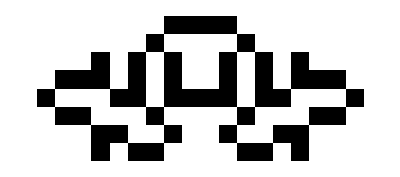
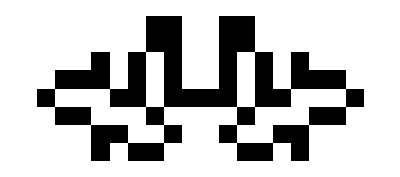
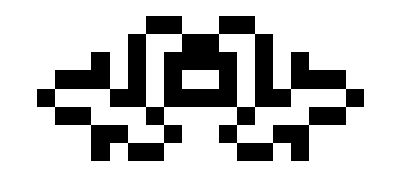
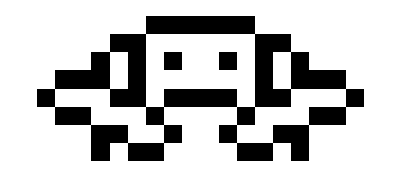
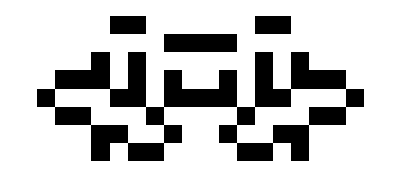
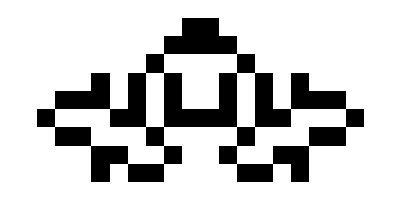
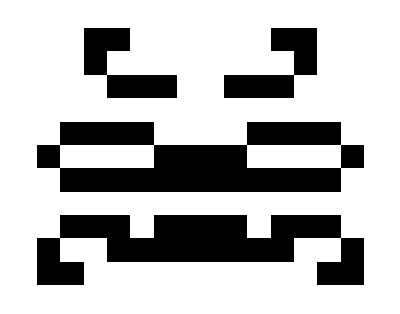
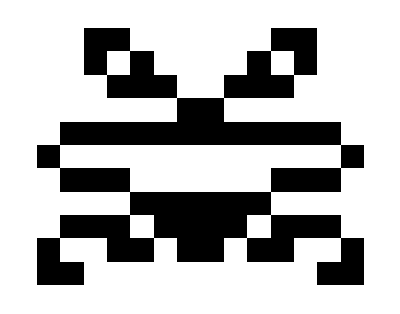
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@Intersection[Values[$LifeParts["Oscillator"]][[397]], Values[$LifeParts["Oscillator"]][[2]]]
```

```mathematica
EdgeList[g2osc][[1]]
```

{104P9,2020,16}->{p27lumpsofmuckhassler,2022,59}

```mathematica
Keys[$LifeParts["Oscillator"]][[2]]
```

104P9

Maybe we should show the matrix of this with the actual parts?

What are some better ways to

#### Tracking a specific part’s usage across time

```mathematica
ReverseSort[CountsBy[Select[Position[mat, 1], #[[1]] != #[[2]]&], First]]
```

<|134→159,184→31,665→27,762→23,159→21,742→17,195→16,156→14,745→13,238→12,44→11,223→11,239→11,701→11,149→10,205→10,212→10,746→7,81→6,234→6,574→6,695→5,754→5,79→4,187→4,214→4,737→4,252→3,578→3,2→2,42→2,51→2,53→2,74→2,86→2,124→2,182→2,216→2,220→2,230→2,241→2,249→2,271→2,538→2,733→2,20→1,25→1,31→1,57→1,60→1,78→1,90→1,113→1,126→1,137→1,148→1,152→1,160→1,179→1,218→1,235→1,324→1,402→1,459→1,503→1,507→1,510→1,532→1,536→1,576→1,718→1,723→1,736→1,741→1,744→1,752→1,758→1|>

```mathematica
Keys[$LifeParts["Oscillator"]][[184]]
```

Figure eight

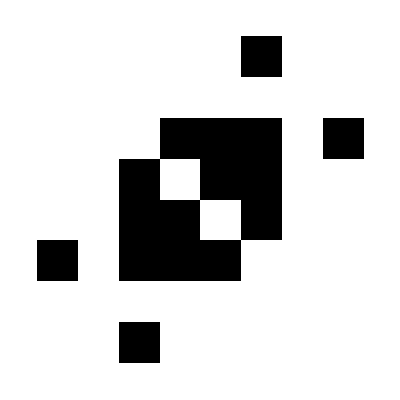
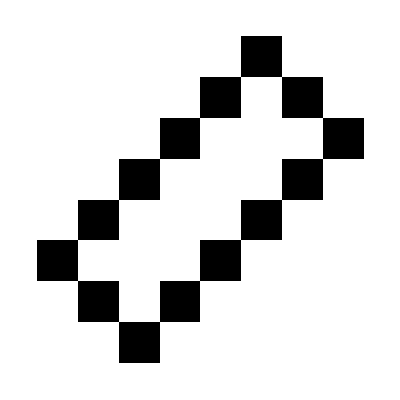
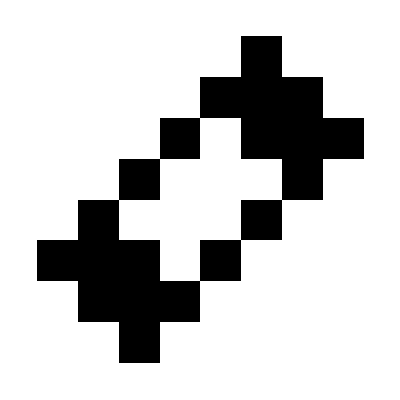
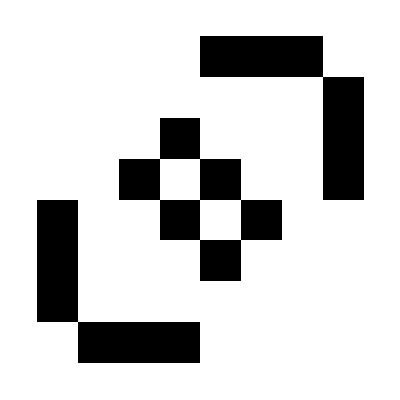
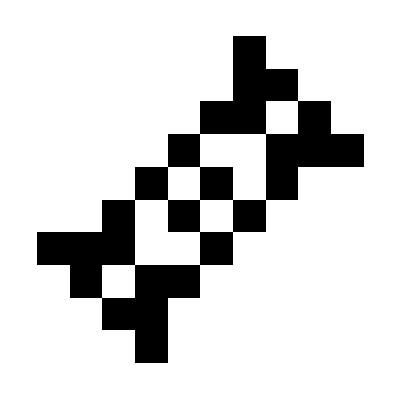
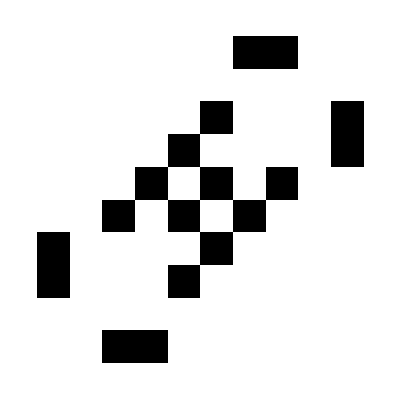
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@$LifeParts["Oscillator"][[184, All]]
```

```mathematica
ArrayPlot3D[ ArrayPad[#, List/@(Floor[({10, 10} - Dimensions[#] )/ 2])]&/@$LifeParts["Oscillator"][[184, 3;;]],Mesh->True]
```

-Graphics3D-

```mathematica
Map[ArrayPlot[#, ImageSize->30]&, $LifeParts["Oscillator"][[Cases[Select[Position[mat, 1], #[[1]] != #[[2]]&], {184, _}][[;;3, 2]]]], {2}]
```

<|Charity's p16→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},p104lumpsofmuckshuttle→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},p104rpentominohassler→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>

### Testing hertz’s oscillator

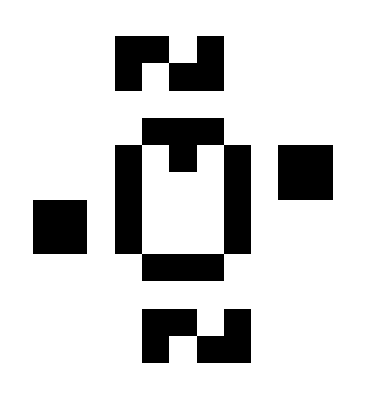
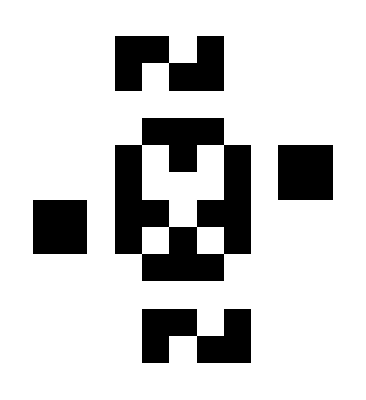
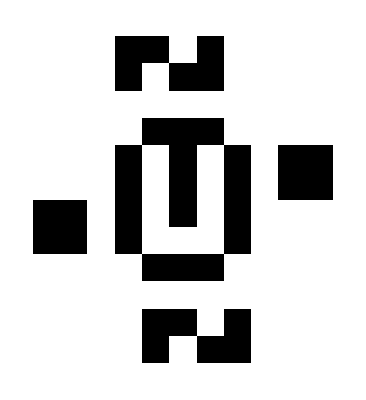
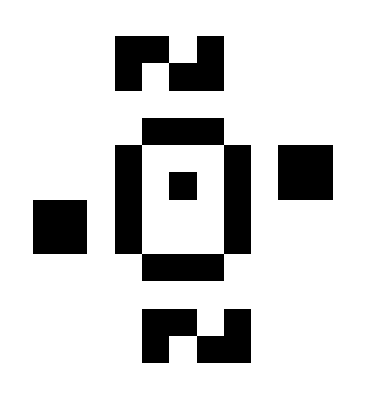
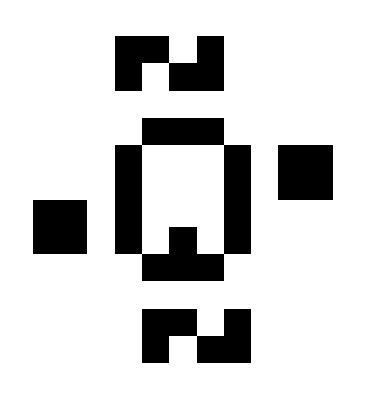
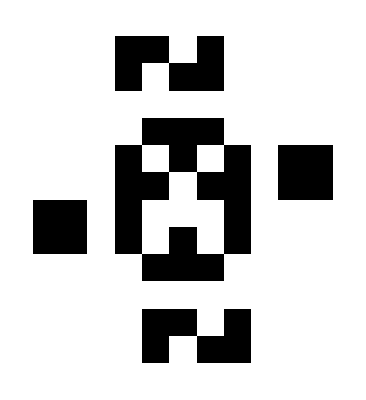
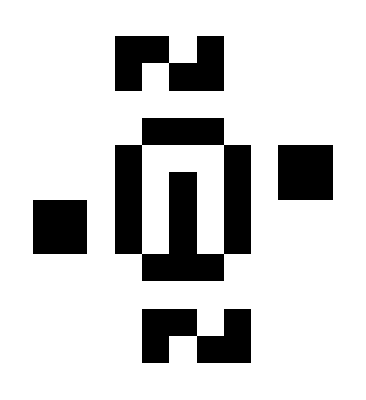
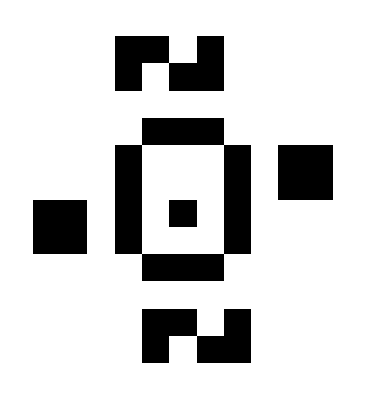
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@CellularAutomaton["GameOfLife", {$LifeData["Hertz oscillator"]["MatrixData"], 0}, 8]
```

### Testing weird period error

```mathematica
Select[<|"a"-> 1, "b"-> 2|>, #[]]
```